```mathematica
kp=5.8*10^4;
e= 1.60217662*10^(-19);
epsilon0:= 8.85*10^(-12);
X=25.0 *10 ^(-6);
y3[r_]:=-((e *kp)/(epsilon0))NIntegrate[Sin[kp(X-x)](-BesselK[1,kp*r]*BesselI[0,kp*R] )((1.878*10^6)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) R ^2/((5*10^(-6))^2)*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Infinity,X},{R,0,r}]
y4[r_]:=-((e *kp)/(epsilon0))NIntegrate[Sin[kp(X-x)](-BesselK[0,kp*R]*BesselI[1,kp*r] )((1.878*10^6)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) R ^2/((5*10^(-6))^2)*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Infinity,X},{R,r,0.1}]
(y3[9.0 *10 ^(-6)]-y4[9.0 *10 ^(-6)])/2
```

3.52839×10^7

```mathematica
Do[Print[Re[(y3[i*10 ^(-6)]+y4[i *10 ^(-6)])/2]],{i,19,35,1}]
```

1.94833×10^7

1.77743×10^7

1.62072×10^7

1.45872×10^7

1.37066×10^7

1.27798×10^7

1.17558×10^7

1.0817×10^7

9.84979×10^6

9.10329×10^6

8.31511×10^6

7.52836×10^6

7.006×10^6

6.51272×10^6

6.04918×10^6

5.6153×10^6

5.21046×10^6

```mathematica
:
```

```mathematica
kpp=5.8*10^4;
kp=1.8341496*10^5;
e= 1.60217662*10^(-19);
epsilon0:= 8.85*10^(-12);
r=0;
y2[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselK[0,kp*R] )((1.878*10^8)/(5*5^2*10^(-18)*(2*Pi)^(1.5)) R*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Infinity,X},{R,0,Infinity}]

y2[0 *10 ^(-6)]
```

3.04541×10^9

```mathematica
kp=1.724*10^5;
e= 1.60217662*10^(-19);
epsilon0= 8.854187817*10^(-12);
r=0*10^(-6);
y[X_]:=-((e *kp^2)/(epsilon0))Integrate[Cos[kp(X-x)](-BesselI[0,r] BesselK[0,R]  )( (1.878*10^6)/(5*5^2*10^(-18)*(2*Pi)^(1.5))*R*Exp[-R^2/(2*(5*10^(-6))^2)-(x)^2/(2*(5*10^(-6))^2)]),{x,-Inf
inity,X},{R,r,2.0*10^(-6)}]


y[0.0 *10^(-6)]
```

-537.819 ∫_0^(2.×10^-6) (0.-2.06142×10^15 ⅈ) ⅇ^(-2.×10^10 R^2) R BesselK[0,R] (1. Erfi[0.609526-(0.+141421. ⅈ) Inf inity]-1. Erfi[0.609526+(0.+141421. ⅈ) Inf inity])ⅆR

```mathematica
FullSimplify[-608.7326896378717 ∫_(1.*^-6)^(2.*^-6) -2.970711237538573*^21 (-4.443255022728844*^-6 ⅇ^(-20000000000 R^2)+(2.0437667391255006*^-6+6.88214269644119*^-22 ⅈ) ⅇ^(-2.*^10 R^2)) R BesselK[0,R]ⅆR]
```

-608.733 ∫_(1.×10^-6)^(2.×10^-6) (1.31996×10^16 ⅇ^(-20000000000 R^2)-(6.07144×10^15+2.04449 ⅈ) ⅇ^(-2.×10^10 R^2)) R BesselK[0,R]ⅆR

```mathematica
BesselK[0,100.0]
```

4.65663×10^-45

```mathematica
points=Table[{x,y[x]},{x,Range[0*10^(-6),65*10^(-6),1*10^(-6)]}];
```

Integrate::ilim: Invalid integration variable or limit(s) in {0,-∞,0}.

Integrate::ilim: Invalid integration variable or limit(s) in {1/1000000,-∞,1/1000000}.

Integrate::ilim: Invalid integration variable or limit(s) in {1/500000,-∞,1/500000}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

```mathematica
RealDigits[5.193512495014662*^9]
```

{{5,1,9,3,5,1,2,4,9,5,0,1,4,6,6,2},10}

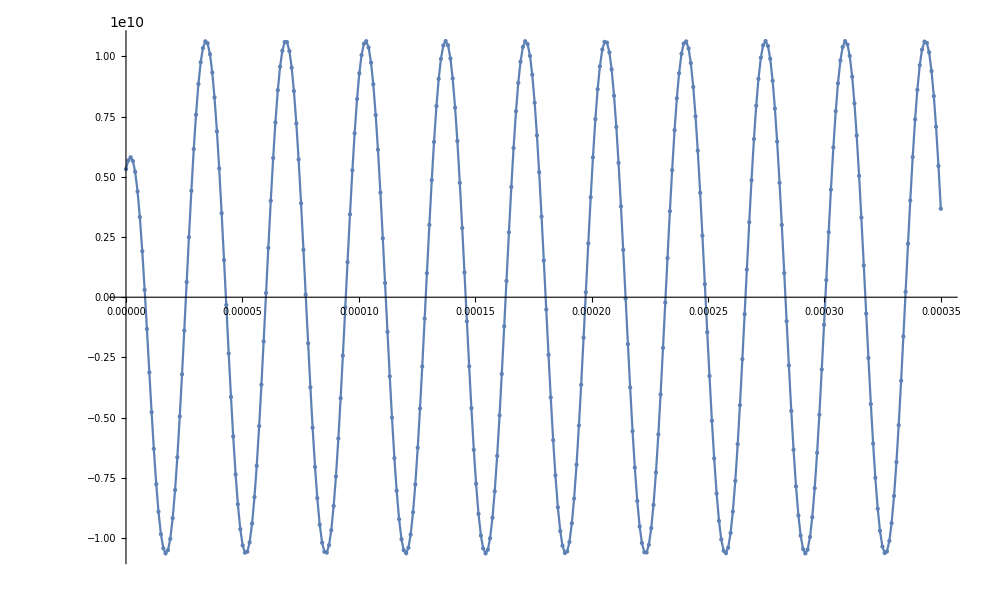

```mathematica
fig=Plot[y[a],{a,0*10 ^(-6),350*10 ^(-6)},Mesh->All,MaxRecursion->0,PlotPoints->350]
```

```mathematica
Do[Print[Re[y2[i*10^(-6)]]],{i,20,100,1}]
```

-5.26559×10^9

-4.61868×10^9

-3.81692×10^9

-2.88716×10^9

-1.86056×10^9

-7.71549×10^8

3.43339×10^8

1.44671×10^9

2.50154×10^9

3.47246×10^9

4.32689×10^9

5.03616×10^9

5.57648×10^9

5.92974×10^9

6.08407×10^9

6.03429×10^9

5.78209×10^9

5.33591×10^9

4.71073×10^9

3.92753×10^9

3.01256×10^9

1.99654×10^9

9.13532×10^8

-2.00118×10^8

-1.30705×10^9

-2.37014×10^9

-3.35372×10^9

-4.22479×10^9

-4.95414×10^9

-5.51728×10^9

-5.89534×10^9

-6.07563×10^9

-6.0521×10^9

-5.82555×10^9

-5.40356×10^9

-4.8003×10^9

-4.03601×10^9

-3.13632×10^9

-2.13142×10^9

-1.05501×10^9

5.67857×10^7

1.16668×10^9

2.23743×10^9

3.23313×10^9

4.12036×10^9

4.86937×10^9

5.45503×10^9

5.85768×10^9

6.06384×10^9

6.06656×10^9

5.86578×10^9

5.46822×10^9

4.88721×10^9

4.14225×10^9

3.25834×10^9

2.26512×10^9

1.19591×10^9

8.65781×10^7

-1.02565×10^9

-2.10348×10^9

-3.11074×10^9

-4.01365×10^9

-4.78191×10^9

-5.38975×10^9

-5.81678×10^9

-6.04868×10^9

-6.07766×10^9

-5.90276×10^9

-5.52984×10^9

-4.97141×10^9

-4.2462×10^9

-3.37855×10^9

-2.39756×10^9

-1.33614×10^9

-2.29894×10^8

8.84064×10^8

1.96836×10^9

2.98663×10^9

3.90471×10^9

4.69179×10^9

5.32148×10^9

```mathematica
Do[Print[Re[y2[i*10^(-6)]]],{i,-20,20,1}]
```

-5.26559×10^9

-5.73607×10^9

-6.01454×10^9

-6.09209×10^9

-5.96687×10^9

-5.64436×10^9

-5.13752×10^9

-4.46667×10^9

-3.6592×10^9

-2.74904×10^9

-1.77571×10^9

-7.82892×10^8

1.83577×10^8

1.07833×10^9

1.85963×10^9

2.49278×10^9

2.95339×10^9

3.22985×10^9

3.32465×10^9

3.25393×10^9

3.04541×10^9

2.73472×10^9

2.36093×10^9

1.96193×10^9

1.57043×10^9

1.21132×10^9

9.00484×10^8

6.45203×10^8

4.45556×10^8

2.96521×10^8

1.90154×10^8

1.17487×10^8

6.99268×10^7

4.00873×10^7

2.21317×10^7

1.17654×10^7

6.02176×10^6

2.96696×10^6

1.40708×10^6

642244.

282102.

1.37802×10^7

1.19833×10^7

1.01461×10^7

8.35224×10^6

6.6761×10^6

5.1756×10^6

3.88754×10^6

2.82666×10^6

1.98798×10^6

1.35142×10^6

887447.

562645.

344241.

203163.

115618.

63424.7

33529.3

17077.

8377.62

3957.91

1800.39

788.417

1.19833×10^7

1.37802×10^7

1.54534×10^7

1.69287×10^7

1.8149×10^7

1.90784×10^7

1.97034×10^7

2.00304×10^7

2.00813×10^7

1.98874×10^7

1.94846×10^7

1.89079×10^7

1.81892×10^7

1.7355×10^7

1.64268×10^7

1.54208×10^7

1.43494×10^7

1.32219×10^7

1.20457×10^7

1.08267×10^7

9.57005×10^6

8.28071×10^6

6.96326×10^6

5.62228×10^6

4.26234×10^6

2.88804×10^6

1.50403×10^6

114951.

-1.27451×10^6

-2.65969×10^6

-4.03593×10^6

-5.39859×10^6

-6.7431×10^6

-8.06492×10^6

-9.35963×10^6

-1.06229×10^7

-1.18504×10^7

-1.3038×10^7

-1.41818×10^7

-1.52779×10^7

-1.63226×10^7

-1.73125×10^7

-1.82441×10^7

-1.91143×10^7

-1.99203×10^7

-2.06593×10^7

-2.13288×10^7

-2.19266×10^7

-2.24506×10^7

-2.28991×10^7

-2.32706×10^7

-2.35639×10^7

-2.37779×10^7

-2.3912×10^7

-2.39656×10^7

-2.39386×10^7

-2.38311×10^7

-2.36435×10^7

-2.33764×10^7

-2.30306×10^7

-2.26074×10^7

-2.21082×10^7

-2.15346×10^7

-2.08886×10^7

-2.01723×10^7

-1.93882×10^7

-1.85389×10^7

-1.76272×10^7

-1.66563×10^7

-1.56294×10^7

-1.45498×10^7

-1.34214×10^7

-1.22478×10^7

-1.10331×10^7

-9.78118×10^6

-8.49641×10^6

-7.18306×10^6

-5.84556×10^6

-4.4884×10^6

-3.11614×10^6

-1.73341×10^6

```mathematica
Do[Print[Re[y2[i*10^(-6)]]],{i,69,120,1}]
```